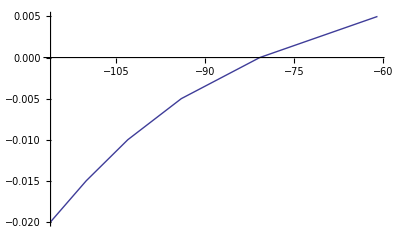

{1.,1.,1.,1.,0.758578,0.1,0.841395,37.1535,9.54993,0.338844,10.,0.912011,1.,165.959,0.0346737,0.870964,1.,1.,1.,1.,1.,1.}

```mathematica
(* test interpolation for calcium *)
VforCa={{-120},{-117.75},{-115.5},{-113.25},{-111},{-108.75},{-106.5},{-104.25},{-102},{-99.7499},{-97.4999},{-95.2499},{-92.9999},{-90.7499},{-88.5},{-86.25},{-84},{-81.75},{-79.5},{-77.25},{-75},{-72.75},{-70.5},{-68.25},{-66},{-63.75},{-61.5},{-59.2501},{-57.0001},{-54.75},{-52.5},{-50.25},{-48},{-45.75},{-43.5},{-41.2502},{-39.0004},{-36.7508},{-34.5014},{-32.2524}};
CaiCa={{0.0529312},{0.0582999},{0.0659793},{0.0769738},{0.0927292},{0.115329},{0.147777},{0.194415},{0.26152},{0.358182},{0.497582},{0.698863},{0.989865},{1.41115},{2.02188},{2.90855},{4.19781},{6.07542},{8.8144},{12.8168},{18.676},{27.2692},{39.8963},{58.4875},{85.9151},{126.461},{186.524},{275.679},{408.277},{605.856},{900.759},{1341.55},{2001.07},{2988.34},{4465.84},{6674.13},{9965.85},{14850.5},{22049},{32551.5}};
CaiPairs=Transpose[{Flatten[VforCa],Flatten[CaiCa]}];
CaiFn=Interpolation[CaiPairs];
(*
VSomaVclamp={{-120},{-117.75},{-115.5},{-113.25},{-111},{-108.75},{-106.5},{-104.25},{-102},{-99.7499},{-97.4999},{-95.25},{-93},{-90.75},{-88.5},{-86.25},{-84},{-81.75},{-79.5},{-77.25},{-75},{-72.75},{-70.5001},{-68.2501},{-66.0001},{-63.7501},{-61.5001},{-59.2501},{-57.0001},{-54.7501},{-52.5001},{-50.25},{-48},{-45.75},{-43.5},{-41.2501},{-39.0002},{-36.7505},{-34.5011},{-32.2519}};
ISomaVclamp={{-0.143434},{-0.134647},{-0.125748},{-0.116712},{-0.107536},{-0.0982398},{-0.0888617},{-0.0794505},{-0.0700554},{-0.0607183},{-0.05147},{-0.0423281},{-0.0332985},{-0.024376},{-0.0155462},{-0.00678636},{0.00193652},{0.0106695},{0.0194827},{0.0284831},{0.0378304},{0.0477406},{0.0584511},{0.0701115},{0.0825886},{0.0952442},{0.106862},{0.114707},{0.111813},{0.0977246},{0.0729124},{0.0417787},{0.0111211},{-0.0075772},{0.00343288},{0.0705888},{0.232454},{0.543871},{1.07947},{1.93357}};
SomaPairs=Transpose[{Flatten[VSomaVclamp],Flatten[ISomaVclamp]*0.10610329539459691}];
*)
gpr={
{1,2,3,4,5,6,7,8,9,10,11},
{2.5*10^-4,0.0001,0.0001,0.002,0.0001,0.1,0.01,3.75*10^-03,0.150,1.5*10^-4,2.0*10^-5},
{2,3,2,1,2,1,1,1,1,2,2},
{"gAR (S/cm2)","gCATA (S/cm2)" ,"gK2 (S/cm2)" , "gKA (S/cm2)" , "gKAHPS (S/cm2)" , "gKDRFS (S/cm2)" ,"gKCFAST (S/cm2)" , "gKM (S/cm2)" , "gNAF2 (S/cm2)" , "gNAPF (S/cm2)" , "gPAS (S/cm2)"}
};
L4ssPts={{-116,-0.02},{-110,-0.015},{-103,-0.01},{-94,-0.005},{-80.8,0},{-61,0.005}};
L4ssPtsDiv100=Transpose[{Transpose[L4ssPts][[1]]*1,Transpose[L4ssPts][[2]]/10.0}];
ListLinePlot[L4ssPts]
gb=10; (* scale for log power *)
Manipulate[Show[Plot[
-Iext*1/1000*0.10610329539459691 +
(gpr[[2]][[1]]*gb^g1 (-Ear+v))/(1+835983.0664036247 ⅇ^(0.18181818181818182 v))+(gpr[[2]][[2]]*gb^g2 (-Ecat+v))/((1+ⅇ^(16+v/5)) (1+0.0008875665735058577 ⅇ^(-0.13513513513513511 v))^2)+(gpr[[2]][[3]]*gb^g3 (-Ek+v))/((1+ⅇ^(1/17 (-10-v))) (1+237.86376961337362 ⅇ^(0.09433962264150944 v)))+(gpr[[2]][[4]]*gb^g4 (-Ek+v))/((1+ⅇ^(13+v/6)) (1+0.0008597890156869497 ⅇ^(-0.11764705882352941 v))^4)+(gpr[[2]][[6]]*1. gb^g6 (-Ek+v))/((1.+0.09557671199708599 ⅇ^(-0.08695652173913043 v))^4)+(gpr[[2]][[8]]*11.90389768996422 ⅇ^(23 v/90) gb^g8 (-1. Ek+v))/(0.01+0.5459815003314423 ⅇ^(v/5)+11.90389768996422 ⅇ^(23 v/90))+(gpr[[2]][[10]]*gb^g10 (-Ena+v))/((1+0.028724639654239423 ⅇ^(-v/10))^3)+(gpr[[2]][[9]]*gb^g9 (-Ena+v))/((1+0.028724639654239423 ⅇ^(-v/10))^3 (1+6011.87847730889 ⅇ^(0.14925373134328357 v)))+gpr[[2]][[11]]*gb^g11 (-Epas+v)+(gpr[[2]][[7]]*9.929194954664954 ⅇ^(v/11) gb^g7 (-1. Ek+v) If[0.004 CaiFn[v]<1,0.004 CaiFn[v],1])/(4.-9.929194954664954 ⅇ^(v/11))+(gpr[[2]][[5]]*gb^g5 (-Ek+v) If[CaiFn[v]<500,CaiFn[v]/50000,0.01])/(0.001+If[CaiFn[v]<500,CaiFn[v]/50000,0.01])

,{v,-120,-40},PlotRange->{{-120,-40},{-0.01,0.01}}],ListLinePlot[L4ssPtsDiv100,PlotStyle->{Orange}]],
{{g1  ,0,gpr[[4]][[1]]},  (-gpr[[3]][[1]]), (  gpr[[3]][[1]])},
{{g2  ,0,gpr[[4]][[2]]},  (-gpr[[3]][[2]]), (  gpr[[3]][[2]])},
{{g3  ,0,gpr[[4]][[3]]},  (-gpr[[3]][[3]]),  (  gpr[[3]][[3]])},
{{g4  ,0,gpr[[4]][[4]]},  (-gpr[[3]][[4]]),  (  gpr[[3]][[4]])},
{{g5  ,0,gpr[[4]][[5]]},  (-gpr[[3]][[5]]),  (  gpr[[3]][[5]])},
{{g6  ,0,gpr[[4]][[6]]},  (-gpr[[3]][[6]]),  ( gpr[[3]][[6]])},
{{g7  ,0,gpr[[4]][[7]]},  (-gpr[[3]][[7]]),  (  gpr[[3]][[7]])},
{{g8  ,0,gpr[[4]][[8]]},  (-gpr[[3]][[8]]),  (  gpr[[3]][[8]])},
{{g9  ,0,gpr[[4]][[9]]},  (-gpr[[3]][[9]]),  (  gpr[[3]][[9]])},
{{g10,0,gpr[[4]][[10]]},(-gpr[[3]][[10]]),( gpr[[3]][[10]])},
{{g11,0,gpr[[4]][[11]]},(-gpr[[3]][[11]]),( gpr[[3]][[11]])},

{{Ear,-40,"Ear (mV)"},-35,-45},
{{Epas,-65,"Epas (mV)"},-50,-80},
{{Ecat,125,"Ecat (mV)"},115,135},
{{Ena,50, "Ena (mV)"},40,60},
{{Ek,-100,"Ek (mV)"},-90,-110},
{{Iext,0,"Iext (pA)"}, -200,60}

]
ListOfEntries={Ek/-100.0,Ena/50.0,Ear/-40.0,Epas/-65.0,gb^g9,gb^g6,gb^g4,gb^g3,gb^g10,gb^g7,gb^g8,gb^g5,1.0,gb^g2,gb^g1,gb^g11,1.0,1.0,1.0,1.0,1.0,1.0}
```